### Utilities

```mathematica
norm[v_]:=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2];
```

### Integrand

#### Definition of E - surfaces

We will consider a two loop toy model integrand with two singularities, factorised in the two loop momenta. The first of the two singularities, associated with the first loop momentum, is pinched. At pinched points, the first loop variable must be collinear to a given direction p. The second, instead, is a proper threshold. Their implicit equations are:

```mathematica
eSurf1[k_,l_]:=norm[k]+norm[k-{0,0,1}]-1
eSurf2[k_,l_]:=norm[l]-1
```

#### Definition of integrand and subtraction

The integrand is then defined to be the ratio of a numerator and the two terms leading to singularities. In order to regularise the first of the two singularities, we construct a subtraction term, obtained by simply approximating the numerator in the collinear limit.

```mathematica
integrand1[k_,l_]:=(E^(-(norm[k]+norm[k-{0,0,1}]-1)^2)((k.{1,1,0})^2+l.k))/(eSurf1[k,l]eSurf2[k,l])

integrand2[k_,l_]:=-(l.k)/(eSurf1[k,l]eSurf2[k,l])

integrand[k_,l_]:=integrand1[k,l]+integrand2[k,l]
```

```mathematica
integrand[{kx,ky,kz},{lx,ly,lz}]
```

-(kx lx+ky ly+kz lz)/((-1+√(kx^2+ky^2+(-1+kz)^2)+√(kx^2+ky^2+kz^2)) (-1+√(lx^2+ly^2+lz^2)))+(ⅇ^(-(-1+√(kx^2+ky^2+(-1+kz)^2)+√(kx^2+ky^2+kz^2))^2) ((kx+ky)^2+kx lx+ky ly+kz lz))/((-1+√(kx^2+ky^2+(-1+kz)^2)+√(kx^2+ky^2+kz^2)) (-1+√(lx^2+ly^2+lz^2)))

### Analysis of deformation field close to pinches and E-surfaces

#### Failure of CT in subtracting subspace behaviour

We can easily check that the subtraction term works nicely in the neighbourhoods of the first singularity only. Both plots of the integrand and explicit expansions confirm this.

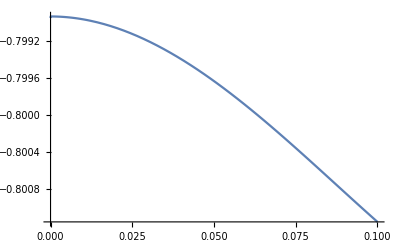

```mathematica
Plot[integrand[{0,eps,0.5},{0.1,0.2,0.3}],{eps,0.0,0.1}]
```

```mathematica
Series[integrand[{0,eps,0.5},{0.1,0.2,0.3}],{eps,0,2}]
```

-0.798934-0.319573 eps^2+O[eps]^3

We now observe that the two singularities intersect. The intersection points, for this specific case, can be described in compact form as

At these points, both terms in the denominator of the integrand vanish. One can wonder if the counter-term, at these intersection points, manages to subtract the divergence coming from both terms in the denominator of the integrand. This is clearly not the case: the pole due to the proper threshold remains.

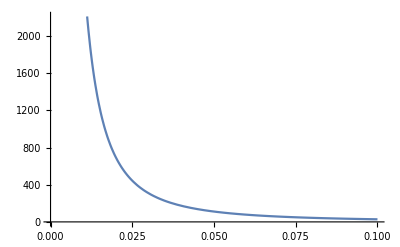

```mathematica
Plot[integrand[{0,eps,0.5},{0.,1,1.9*eps}],{eps,0.0,0.1}]
```

```mathematica
Series[integrand1[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}],{eps,0,2}]
```

0.166667/eps^3+0.423611/eps^2+1.36314/eps-0.00899402+0.899544 eps-3.13698 eps^2+O[eps]^3

```mathematica
Series[integrand2[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}],{eps,0,2}]
```

-0.166667/eps^3-0.423611/eps^2-0.69647/eps-0.296562-0.530331 eps+0.743365 eps^2+O[eps]^3

```mathematica
Series[integrand[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}],{eps,0,2}]
```

0.666667/eps-0.305556+0.369213 eps-2.39361 eps^2+O[eps]^3

#### Need for pinch dampening to avoid inclusion of complex poles

Since the pole due to the proper threshold remains, one is lead to the conclusion that a contour deformation must be active at this intersection point, and deform around the remaining pole. However, a general contour deformation, if not properly constructed, can be shown to pick up poles in the neighbourhood of pinch points. It would seem, actually, that in order not to pick up poles, that the deformation must go to zero on pinches.
We construct two deformation fields: one that is suppressed on pinches and one that is not:

```mathematica
pinchCheck1[k_,l_,m_]:=eSurf1[k,l]^2/(eSurf1[k,l]^2+m^2)

kappa[k_,l_]:=0.7  pinchCheck1[k,l,0.069]{k-0.05,l-0.05}
kappan[k_,l_]:=0.7  {k-0.05,l-0.05}
```

```mathematica
defo[k_,l_]:={k,l}-I kappa[k,l]
defon[k_,l_]:={k,l}-I kappan[k,l]
```

In this first plot, constructed with a deformation that is not suppressed near pinch points, we can see that at the pinch point, the imaginary part induced by the deformation is zero (as expected), while the real part is negative. This is typically a sign that a pole has been included inside the contour, and that the deformation is not satisfying the proper constraints.

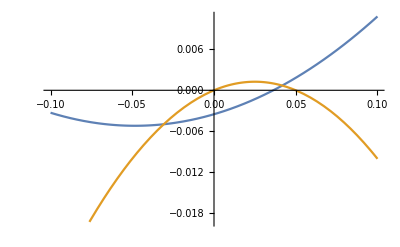

```mathematica
Plot[{Re[eSurf1[defon[{0,eps,0.5},{0.1,0.2,0.3}][[1]],defon[{0,eps,0.5},{0.1,0.2,0.3}][[2]]]],Im[eSurf1[defon[{0,eps,0.5},{0.1,0.2,0.3}][[1]],defon[{0,eps,0.5},{0.1,0.2,0.3}][[2]]]]},{eps,-0.1,0.1}]
```

In this second plot, constructed with a deformation  that is suppressed near pinch points, we can see that the deformation clearly does not include any pinch point.

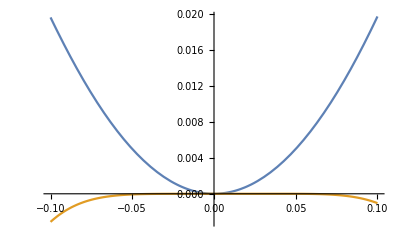

```mathematica
Plot[{Re[eSurf1[defo[{0,eps,0.5},{0.1,0.2,0.3}][[1]],defo[{0,eps,0.5},{0.1,0.2,0.3}][[2]]]],Im[eSurf1[defo[{0,eps,0.5},{0.1,0.2,0.3}][[1]],defo[{0,eps,0.5},{0.1,0.2,0.3}][[2]]]]},{eps,-0.1,0.1}]
```

#### Failure of deformation with no subspace treatment

The dampening is needed in order to not include poles, but a non zero contour deformation is needed to regulate the proper threshold. This seem to lead to a contradiction. Indeed, we can see that the deformation with dampening does not regulate the threshold at the intersection with pinches anymore

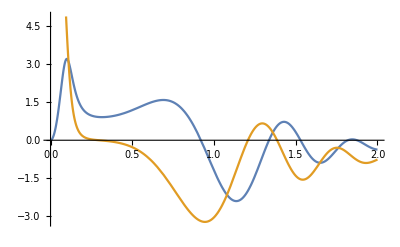

```mathematica
Plot[{Im[integrand[defo[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[1]],defo[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[2]]]],Re[integrand[defo[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[1]],defo[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[2]]]]},{eps,0,2}]
```

```mathematica
Series[integrand[defo[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[1]],defo[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[2]]],{eps,0,2}]
```

(0.666667+0. ⅈ)/eps-(0.305556+0. ⅈ)+(0.369213+0. ⅈ) eps-(2.39361-517.353 ⅈ) eps^2+O[eps]^3

while the deformation without dampening does regulate the threshold properly, even at the intersection with pinches

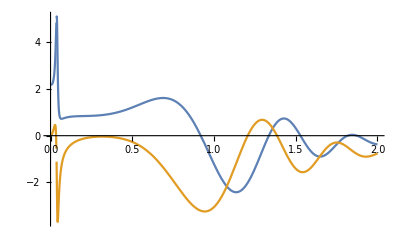

```mathematica
Plot[{Im[integrand[defon[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[1]],defon[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[2]]]],Re[integrand[defon[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[1]],defon[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[2]]]]},{eps,0,2}]
```

```mathematica
Series[integrand[defon[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[1]],defon[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[2]]],{eps,0,2}]
```

(0.00136683+2.1832 ⅈ)+(2.57505-1.83431 ⅈ) eps+(619.251+225.071 ⅈ) eps^2+O[eps]^3

#### Deformation with subspace treatment

How do we solve this apparent contradiction? The solution is to have a subspace treatment for pinches. To the dampened deformation we add a second source which is collinear to p in the first loop variable. Since the source is exactly collinear in the first loop variable, it satisfies the complex pole constraint automatically. Furthermore, we can choose the right source in the second loop variable, so that it actually regulates correctly the proper threshold.

```mathematica
kappaSub[k_,l_]:=0.7*(pinchCheck1[k,l,0.069]*{k-0.05,l-0.05}+{k-{0,0,0.5},l-0.1})

defoSub[k_,l_]:={k,l}-I*kappaSub[k,l]
```

Indeed, we can see that the proper threshold, at the intersection with the pinch, is properly regulated

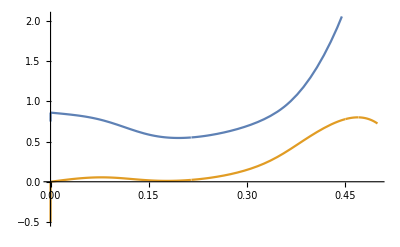

```mathematica
Plot[{Im[integrand[defoSub[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[1]],defoSub[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[2]]]],Re[integrand[defoSub[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[1]],defoSub[{0,eps,0.5},{1/Sqrt[2],1/2+eps,1/2+0.5*eps}][[2]]]]},{eps,0,0.5}]
```

and that no extra pole is included inside the contour.

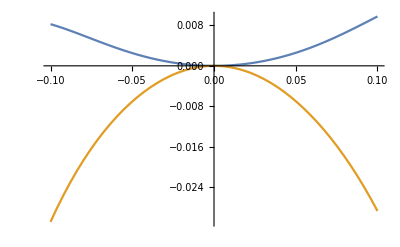

```mathematica
Plot[{Re[eSurf1[defoSub[{0,eps,0.5},{0.1,0.2,0.3}][[1]],defoSub[{0,eps,0.5},{0.1,0.2,0.3}][[2]]]],Im[eSurf1[defoSub[{0,eps,0.5},{0.1,0.2,0.3}][[1]],defoSub[{0,eps,0.5},{0.1,0.2,0.3}][[2]]]]},{eps,-0.1,0.1}]
```

#### Finding a deformation sources for the subspace treatment is a convex problem

Finally, we want to show that finding a deformation source corresponding to the subspace treatment described above can be reduced to a convex optimisation problem. This is very easy to show. Consider the convex optimisation problem

The radial vector field we added to the dampened deformation is centered at an approximate solution of this convex optimisation problem.